# Initialization

```mathematica
HaToeV=27.21138602;
```

```mathematica
SetDirectory["~/Dropbox/Manuscripts/Tmatrix/Data"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,mathpazo,xcolor,bm,mhchem}"}];
```

# Helium-like ions

#### H^-/aug-cc-pVQZ

```mathematica
H$AVQZ$BSEGW$1={3.544803,6.664916};
H$AVQZ$dBSEGW$1={3.477673,6.417843};
H$AVQZ$BSEGW$3={1.924462,5.015223};
H$AVQZ$dBSEGW$3={1.645051,4.641375};
```

```mathematica
H$AVQZ$BSEGT$1={3.076687,6.195034};
H$AVQZ$dBSEGT$1={3.238214,6.211650};
H$AVQZ$BSEGT$3={2.042753,4.455234};
H$AVQZ$dBSEGT$3={1.749067,4.467813};
```

```mathematica
H$AVQZ$FCI$1={2.92693343,5.91171092};
H$AVQZ$FCI$3={1.95653920,5.02369423};
```

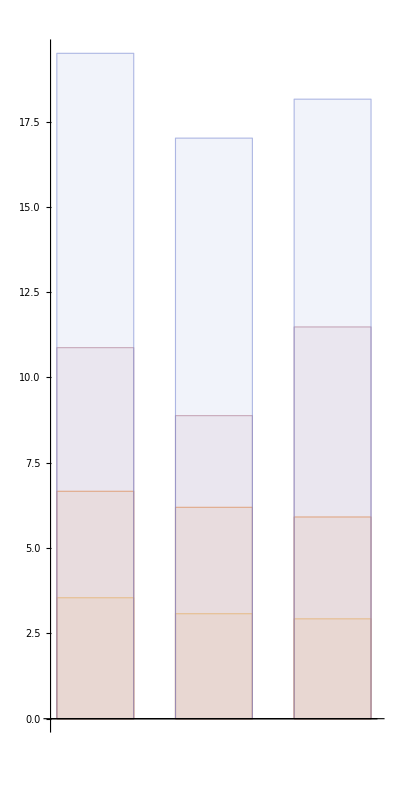

```mathematica
BarChart[{H$AVQZ$BSEGW$1,H$AVQZ$BSEGT$1,H$AVQZ$FCI$1},ChartLayout->"Overlapped",ChartStyle->Opacity[0.1],AspectRatio->2]
```

#### He/aug-cc-pVQZ

```mathematica
He$AVQZ$BSEGW$1={21.135455,24.260667};
He$AVQZ$dBSEGW$1={21.121553,24.217977};
He$AVQZ$BSEGW$3={19.829721,22.853260};
He$AVQZ$dBSEGW$3={19.747778,22.769397};
```

```mathematica
He$AVQZ$BSEGT$1={21.047638,24.358335};
He$AVQZ$dBSEGT$1={21.036042,24.307115};
He$AVQZ$BSEGT$3={20.000952,22.897296};
He$AVQZ$dBSEGT$3={19.958898,22.846260};
```

```mathematica
He$AVQZ$FCI$1={20.82451590,23.90793935};
He$AVQZ$FCI$3={19.87191393,23.00154067};
```

#### Li^+/aug-cc-pVQZ

```mathematica
Li$AVQZ$BSEGW$1={,,,};
Li$AVQZ$dBSEGW$1={,,,};
Li$AVQZ$BSEGW$3={,,,};
Li$AVQZ$dBSEGW$3={,,,};
```

```mathematica
Li$AVQZ$BSEGT$1={,,,};
Li$AVQZ$dBSEGT$1={,,,};
Li$AVQZ$BSEGT$3={,,,};
Li$AVQZ$dBSEGT$3={,,,};
```

```mathematica
Li$AVQZ$FCI$1={,,,};
Li$AVQZ$FCI$3={,,,};
```

# H_2/cc-pVDZ

## Singlets & Triplets

### Loading data

```mathematica
FCI1=Import["h2_cc-pvtz_fci_singlets.dat"];
BSE$GT1=Import["h2_cc-pvtz_bse@gt_singlets.dat"];
BSE$GW1=Import["h2_cc-pvtz_bse@gw_singlets.dat"];
dBSE$GT1=Import["h2_cc-pvtz_dbse@gt_singlets.dat"];
dBSE$GW1=Import["h2_cc-pvtz_dbse@gw_singlets.dat"];
```

```mathematica
FCI3=Import["h2_cc-pvtz_fci_triplets.dat"];
BSE$GT3=Import["h2_cc-pvtz_bse@gt_triplets.dat"];
BSE$GW3=Import["h2_cc-pvtz_bse@gw_triplets.dat"];
dBSE$GT3=Import["h2_cc-pvtz_dbse@gt_triplets.dat"];
dBSE$GW3=Import["h2_cc-pvtz_dbse@gw_triplets.dat"];
```

### Plotting stuff

```mathematica
singlets=Show[{
ListPlot[
{Callout[FCI1⟦;;,{1,2}⟧,"B ^1Σ_u^+"],Callout[FCI1⟦;;,{1,3}⟧,"F ^1Σ_g^+"],Callout[FCI1⟦;;,{1,4}⟧,"B' ^1Σ_u^+"],Callout[FCI1⟦;;,{1,5}⟧,"E ^1Σ_g^+"],Callout[FCI1⟦;;,{1,6}⟧,"C ^1Π_u"]}
,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},AspectRatio->1.5,PlotRange->{All,{5,30}},
FrameLabel->{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],MaTeX["\\text{Singlet excitation energy (eV)}",FontSize->20]},
ImageSize->400,PlotStyle->Directive[{Black,Opacity[0.7],Thickness[0.01]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{FCI}",FontSize->20]},GridLines->Automatic]
,
ListPlot[
{BSE$GW1⟦;;,{1,2}⟧,BSE$GW1⟦;;,{1,3}⟧,BSE$GW1⟦;;,{1,4}⟧,BSE$GW1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0W_0$}",FontSize->20]}]
,
ListPlot[
{BSE$GT1⟦;;,{1,2}⟧,BSE$GT1⟦;;,{1,3}⟧,BSE$GT1⟦;;,{1,4}⟧,BSE$GT1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20]}]
}]
```

-Graphics-

```mathematica
triplets=Show[{
ListPlot[
{Callout[FCI3⟦;;,{1,2}⟧,"b ^3Σ_u^+"],Callout[FCI3⟦;;,{1,3}⟧,"a ^3Σ_g^+"],Callout[FCI3⟦;;,{1,4}⟧,"e ^3Σ_u^+"],Callout[FCI3⟦;;,{1,5}⟧,"c ^3Π_u"],Callout[FCI3⟦;;,{1,6}⟧,"c ^3Π_u"]}
,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},AspectRatio->1.5,PlotRange->{All,{0,25}},
FrameLabel->{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],MaTeX["\\text{Triplet excitation energy (eV)}",FontSize->20]},
ImageSize->400,PlotStyle->Directive[{Black,Opacity[0.7],Thickness[0.01]}],PlotMarkers->"OpenMarkers",Joined->True,GridLines->Automatic]
,
ListPlot[
{BSE$GW3⟦;;,{1,2}⟧,BSE$GW3⟦;;,{1,3}⟧,BSE$GW3⟦;;,{1,4}⟧,BSE$GW3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True]
,
ListPlot[
{BSE$GT3⟦;;,{1,2}⟧,BSE$GT3⟦;;,{1,3}⟧,BSE$GT3⟦;;,{1,4}⟧,BSE$GT3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True]
}]
```

-Graphics-

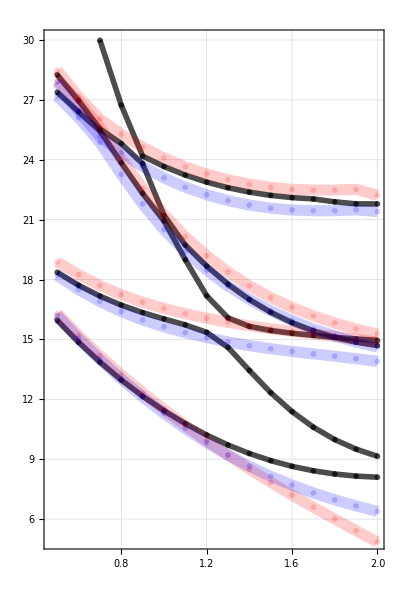
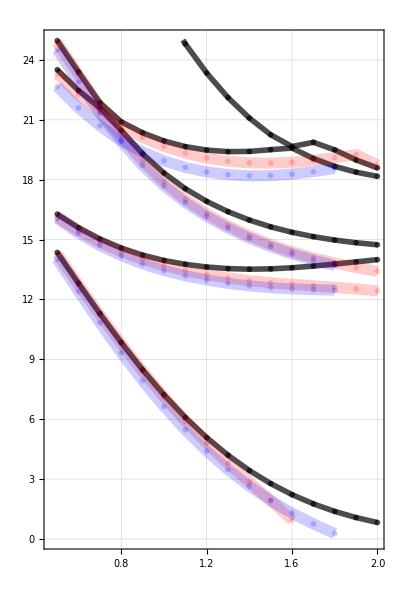
-Graphics- | -Graphics-

```mathematica
Grid[{{singlets,triplets}}]
Export["H2.pdf",%];
```

### Gap

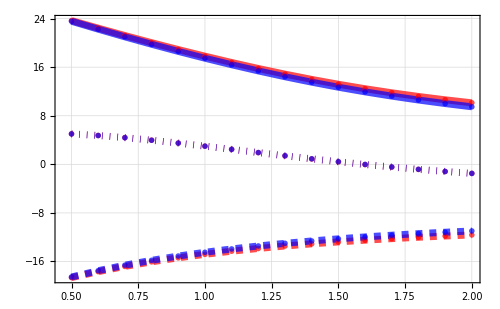

```mathematica
Gap=Import["h2_cc-pvtz_gap.dat"];ListPlot[{Gap⟦;;,{1,2}⟧,Gap⟦;;,{1,5}⟧,Gap⟦;;,{1,3}⟧,Gap⟦;;,{1,6}⟧,Gap⟦;;,{1,4}⟧,Gap⟦;;,{1,7}⟧},Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},PlotRange->{All,All},
FrameLabel->{MaTeX["R_{\\ce{H-H}}~(\\AA)",FontSize->20],MaTeX["\\text{One-electron energy (eV)}",FontSize->20]},
ImageSize->500,
PlotStyle->{{Red,Dashed,Opacity[0.7],Thickness[0.01]},{Blue,Dashed,Opacity[0.7],Thickness[0.01]},
{Red,Dotted,Opacity[0.7],Thickness[0.01]},{Blue,Dotted,Opacity[0.7],Thickness[0.01]},
{Red,Opacity[0.7],Thickness[0.01]},{Blue,Opacity[0.7],Thickness[0.01]}},
PlotMarkers->"OpenMarkers",Joined->True,
PlotLegends->{MaTeX["\\text{HOMO@$G_0W_0$}",FontSize->20],MaTeX["\\text{HOMO@$G_0T_0$}",FontSize->20],
MaTeX["\\text{LUMO@$G_0W_0$}",FontSize->20],MaTeX["\\text{LUMO@$G_0T_0$}",FontSize->20],
MaTeX["\\text{Gap@$G_0W_0$}",FontSize->20],MaTeX["\\text{Gap@$G_0T_0$}",FontSize->20]},
GridLines->Automatic]
Export["H2_gap.pdf",%];
```

# BeH_2/cc-pVDZ

## Singlets & Triplets

### Loading data for singlets

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

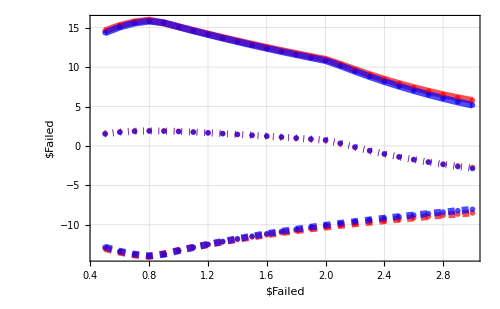

```mathematica
FCI1=Import["beh2_cc-pvdz_fci_singlets.dat"];
BSE$GT1=Import["beh2_cc-pvdz_bse@gt_singlets.dat"];
BSE$GW1=Import["beh2_cc-pvdz_bse@gw_singlets.dat"];
dBSE$GT1=Import["beh2_cc-pvdz_dbse@gt_singlets.dat"];
dBSE$GW1=Import["beh2_cc-pvdz_dbse@gw_singlets.dat"];
```

### Plotting stuff for singlets

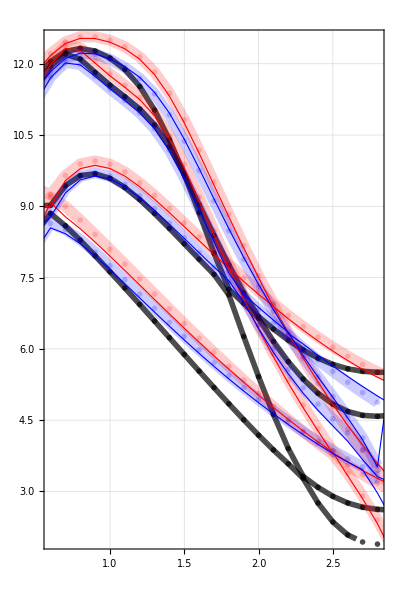

```mathematica
singlets=Show[{
ListPlot[
{FCI1⟦;;,{1,2}⟧,FCI1⟦;;,{1,3}⟧,FCI1⟦;;,{1,4}⟧,FCI1⟦;;,{1,5}⟧}
,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},AspectRatio->1.5,PlotRange->{{0.6,2.8},{2,12.5}},
FrameLabel->{MaTeX["R_{\\ce{Be-H}}~(\\AA)",FontSize->20],MaTeX["\\text{Singlet excitation energy (eV)}",FontSize->20]},
ImageSize->400,PlotStyle->Directive[{Black,Opacity[0.7],Thickness[0.01]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{FCI}",FontSize->20]},GridLines->Automatic]
,
ListPlot[
{BSE$GW1⟦;;,{1,2}⟧,BSE$GW1⟦;;,{1,3}⟧,BSE$GW1⟦;;,{1,4}⟧,BSE$GW1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0W_0$}",FontSize->20]}]
,
ListPlot[
{BSE$GT1⟦;;,{1,2}⟧,BSE$GT1⟦;;,{1,3}⟧,BSE$GT1⟦;;,{1,4}⟧,BSE$GT1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20]}]
,
ListPlot[
{dBSE$GW1⟦;;,{1,2}⟧,dBSE$GW1⟦;;,{1,3}⟧,dBSE$GW1⟦;;,{1,4}⟧,dBSE$GW1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[1.0],Thickness[0.002]}],PlotMarkers->None,Joined->True,PlotLegends->{MaTeX["\\text{dBSE@$G_0T_0$}",FontSize->20]}]
,
ListPlot[
{dBSE$GT1⟦;;,{1,2}⟧,dBSE$GT1⟦;;,{1,3}⟧,dBSE$GT1⟦;;,{1,4}⟧,dBSE$GT1⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[1.0],Thickness[0.002]}],PlotMarkers->None,Joined->True,PlotLegends->{MaTeX["\\text{dBSE@$G_0T_0$}",FontSize->20]}]
}]
```

### Loading data for triplets

```mathematica
FCI3=Import["beh2_cc-pvdz_fci_triplets.dat"];
BSE$GT3=Import["beh2_cc-pvdz_bse@gt_triplets.dat"];
BSE$GW3=Import["beh2_cc-pvdz_bse@gw_triplets.dat"];
dBSE$GT3=Import["beh2_cc-pvdz_dbse@gt_triplets.dat"];
dBSE$GW3=Import["beh2_cc-pvdz_dbse@gw_triplets.dat"];
```

### Plotting stuff for triplets

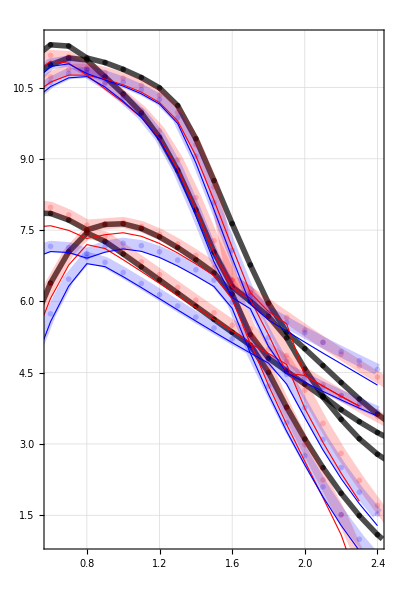

```mathematica
triplets=Show[{
ListPlot[
{FCI3⟦;;,{1,2}⟧,FCI3⟦;;,{1,3}⟧,FCI3⟦;;,{1,4}⟧,FCI3⟦;;,{1,5}⟧}
,Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},AspectRatio->1.5,PlotRange->{{0.6,2.4},{1,11.5}},
FrameLabel->{MaTeX["R_{\\ce{Be-H}}~(\\AA)",FontSize->20],MaTeX["\\text{Triplet excitation energy (eV)}",FontSize->20]},
ImageSize->400,PlotStyle->Directive[{Black,Opacity[0.7],Thickness[0.01]}],PlotMarkers->"OpenMarkers",Joined->True,GridLines->Automatic]
,
ListPlot[
{BSE$GW3⟦;;,{1,2}⟧,BSE$GW3⟦;;,{1,3}⟧,BSE$GW3⟦;;,{1,4}⟧,BSE$GW3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True]
,
ListPlot[
{BSE$GT3⟦;;,{1,2}⟧,BSE$GT3⟦;;,{1,3}⟧,BSE$GT3⟦;;,{1,4}⟧,BSE$GT3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thickness[0.02]}],PlotMarkers->"OpenMarkers",Joined->True]
,
ListPlot[
{dBSE$GW3⟦;;,{1,2}⟧,dBSE$GW3⟦;;,{1,3}⟧,dBSE$GW3⟦;;,{1,4}⟧,dBSE$GW3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[1.0],Thickness[0.002]}],PlotMarkers->None,Joined->True]
,
ListPlot[
{dBSE$GT3⟦;;,{1,2}⟧,dBSE$GT3⟦;;,{1,3}⟧,dBSE$GT3⟦;;,{1,4}⟧,dBSE$GT3⟦;;,{1,5}⟧}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[1.0],Thickness[0.002]}],PlotMarkers->None,Joined->True]
}]
```

### Main graph

```mathematica
Grid[{{singlets,triplets}}]
Export["BeH2.pdf",%];
```

-Graphics- | -Graphics-

### Gap

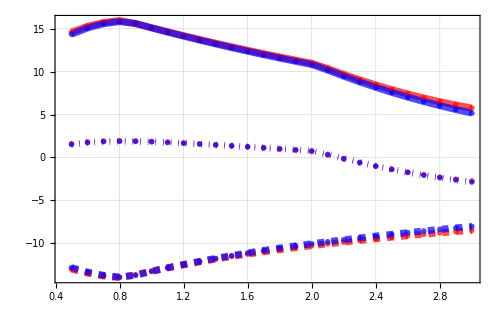

```mathematica
Gap=Import["beh2_cc-pvdz_gap.dat"];
ListPlot[{Gap⟦;;,{1,2}⟧,Gap⟦;;,{1,5}⟧,Gap⟦;;,{1,3}⟧,Gap⟦;;,{1,6}⟧,Gap⟦;;,{1,4}⟧,Gap⟦;;,{1,7}⟧},Frame->True,FrameStyle->Directive[{Black,Thick}],BaseStyle->{Thick,16},PlotRange->{All,All},
FrameLabel->{MaTeX["R_{\\ce{Be-H}}~(\\AA)",FontSize->20],MaTeX["\\text{One-electron energy (eV)}",FontSize->20]},
ImageSize->500,
PlotStyle->{{Red,Dashed,Opacity[0.7],Thickness[0.01]},{Blue,Dashed,Opacity[0.7],Thickness[0.01]},
{Red,Dotted,Opacity[0.7],Thickness[0.005]},{Blue,Dotted,Opacity[0.7],Thickness[0.01]},
{Red,Opacity[0.7],Thickness[0.01]},{Blue,Opacity[0.7],Thickness[0.01]}},
PlotMarkers->"OpenMarkers",Joined->True,
PlotLegends->{MaTeX["\\text{HOMO@$G_0W_0$}",FontSize->20],MaTeX["\\text{HOMO@$G_0T_0$}",FontSize->20],
MaTeX["\\text{LUMO@$G_0W_0$}",FontSize->20],MaTeX["\\text{LUMO@$G_0T_0$}",FontSize->20],
MaTeX["\\text{Gap@$G_0W_0$}",FontSize->20],MaTeX["\\text{Gap@$G_0T_0$}",FontSize->20]},
GridLines->Automatic]
Export["BeH2_gap.pdf",%];
```

# H_4/STO-6G

## Singlets & Triplets

### Loading data for singlets

```mathematica
BSE$GW1=Import["h4_sto-6g_bse@gw_singlets.dat"];
BSE$GT1=Import["h4_sto-6g_bse@gt_singlets.dat"];
```

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

Ghostscript is not found at /usr/local/bin/gs

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

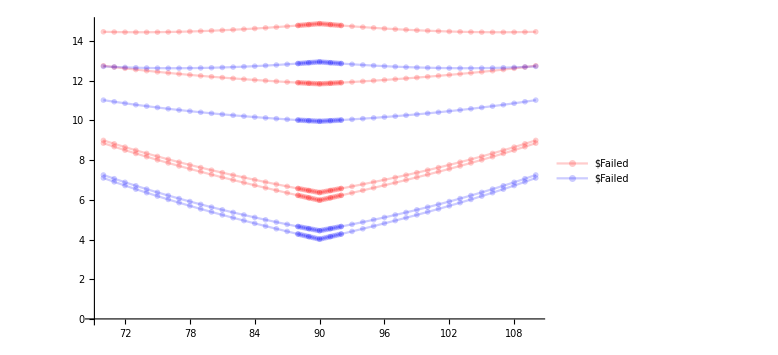

```mathematica
Show[{
ListPlot[
{BSE$GW1⟦;;,{1,2}⟧//Sort,BSE$GW1⟦;;,{1,3}⟧//Sort,BSE$GW1⟦;;,{1,4}⟧//Sort,BSE$GW1⟦;;,{1,5}⟧//Sort}
,ImageSize->Large,PlotStyle->Directive[{Red,Opacity[0.2],Thick}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20]}]
,
ListPlot[
{BSE$GT1⟦;;,{1,2}⟧//Sort,BSE$GT1⟦;;,{1,3}⟧//Sort,BSE$GT1⟦;;,{1,4}⟧//Sort,BSE$GT1⟦;;,{1,5}⟧//Sort}
,ImageSize->Large,PlotStyle->Directive[{Blue,Opacity[0.2],Thick}],PlotMarkers->"OpenMarkers",Joined->True,PlotLegends->{MaTeX["\\text{BSE@$G_0T_0$}",FontSize->20]}]
}]
```

# Molecules

## cc-pVDZ

### H_2

```mathematica
TableForm[{
{"CIS",
14.065864,21.454191,32.284171,40.303503,56.580511,
10.080616,16.746878,26.604984,33.631206,52.423452},
{"CIS(D)",
14.021613,21.579581,31.926961,40.609175,54.243320,
10.577439,17.398033,27.031493,34.238907,52.998869},
{"TDHF",
13.901098,21.318637,32.033486,40.165190,56.529326,
9.627843,16.561107,26.372633,33.465327,52.371924},
{"BSE2@GF2",
13.914508,21.455711,31.693250,40.552290,57.127380,
10.831007,17.420570,26.585834,34.018020,53.861968},
{"BSE@GW",
14.117232,21.939179,32.064543,40.972062,57.792359,
10.537991,17.385732,26.519496,34.395254,54.160836},
{"BSE@GT",
13.966021,20.677946,31.001618,39.463691,55.000066,
10.109375,17.123568,26.269322,33.220696,51.735900},
{"FCI",
13.91369464,21.39557466,29.37264199,30.99058559,38.18622237},
}]
```

CIS | 14.0659 | 21.4542 | 32.2842 | 40.3035 | 56.5805 | 10.0806 | 16.7469 | 26.605 | 33.6312 | 52.4235
CIS(D) | 14.0216 | 21.5796 | 31.927 | 40.6092 | 54.2433 | 10.5774 | 17.398 | 27.0315 | 34.2389 | 52.9989
TDHF | 13.9011 | 21.3186 | 32.0335 | 40.1652 | 56.5293 | 9.62784 | 16.5611 | 26.3726 | 33.4653 | 52.3719
BSE2@GF2 | 13.9145 | 21.4557 | 31.6933 | 40.5523 | 57.1274 | 10.831 | 17.4206 | 26.5858 | 34.018 | 53.862
BSE@GW | 14.1172 | 21.9392 | 32.0645 | 40.9721 | 57.7924 | 10.538 | 17.3857 | 26.5195 | 34.3953 | 54.1608
BSE@GT | 13.966 | 20.6779 | 31.0016 | 39.4637 | 55.0001 | 10.1094 | 17.1236 | 26.2693 | 33.2207 | 51.7359
FCI | 13.9137 | 21.3956 | 29.3726 | 30.9906 | 38.1862 |  |  |  |  | 
Null |  |  |  |  |  |  |  |  |  |

### HF

```mathematica
TableForm[{
{"CIS",
11.927542,16.435595,26.419791,31.788879,38.216870,
11.060308,13.524015,25.670946,26.876940,33.391345},
{"CIS(D)",
10.497127,15.441725,24.600865,30.805391,39.318508,
9.912448,13.578188,24.060136,26.478071,33.943117},
{"TDHF",
11.861151,16.286058,26.352757,31.590420,38.074261,
10.913120,13.050767,25.573802,26.506647,32.873095},
{"BSE@GW",
10.926878,15.753072,24.720999,30.746999,35.465521,
10.172969,13.319056,23.977133,26.006407,32.999729},
{"dBSE@GW",
10.837108,15.697149,24.596569,30.615649,35.376265,
10.044228,13.153493,23.833822,25.780836,32.631516},
{"BSE@GT",
9.758203,14.984132,23.542331,29.470786,34.795349,
9.075224,12.236212,22.906122,24.936420,30.943929},
{"dBSE@GT",
9.726293,14.922890,23.499276,29.435810,34.763581,
9.010619,12.155468,22.835853,24.846836,30.705544},
{"FCI",
10.80153193,15.64647025,24.77206998,,,
,,,,}
}]
```

CIS | 11.9275 | 16.4356 | 26.4198 | 31.7889 | 38.2169 | 11.0603 | 13.524 | 25.6709 | 26.8769 | 33.3913
CIS(D) | 10.4971 | 15.4417 | 24.6009 | 30.8054 | 39.3185 | 9.91245 | 13.5782 | 24.0601 | 26.4781 | 33.9431
TDHF | 11.8612 | 16.2861 | 26.3528 | 31.5904 | 38.0743 | 10.9131 | 13.0508 | 25.5738 | 26.5066 | 32.8731
BSE@GW | 10.9269 | 15.7531 | 24.721 | 30.747 | 35.4655 | 10.173 | 13.3191 | 23.9771 | 26.0064 | 32.9997
dBSE@GW | 10.8371 | 15.6971 | 24.5966 | 30.6156 | 35.3763 | 10.0442 | 13.1535 | 23.8338 | 25.7808 | 32.6315
BSE@GT | 9.7582 | 14.9841 | 23.5423 | 29.4708 | 34.7953 | 9.07522 | 12.2362 | 22.9061 | 24.9364 | 30.9439
dBSE@GT | 9.72629 | 14.9229 | 23.4993 | 29.4358 | 34.7636 | 9.01062 | 12.1555 | 22.8359 | 24.8468 | 30.7055
FCI | 10.8015 | 15.6465 | 24.7721 | Null | Null | Null | Null | Null | Null | Null

### HCl

```mathematica
TableForm[{
{"FCI",
8.21182141,13.26279653,16.74274986,,,
,,,,},
{"CIS",
8.741521,13.774466,17.354388,21.944706,22.537235,
7.805226,10.257723,16.371017,18.592396,19.774495},
{"CIS(D)",
8.398608,13.473052,16.979739,21.970770,22.456364,
7.732548,10.604388,16.191104,19.003426,20.419651},
{"TDHF",
8.682287,13.609600,17.297169,21.830684,22.519372,
7.653963,9.765757,16.268019,18.421696,19.511430},
{"BSE@GW",
8.374432,13.447500,16.781919,21.815746,22.242675,
7.570595,10.442022,15.839855,18.629507,20.563855},
{"dBSE@GW",
8.279701,13.350442,16.661571,21.636009,22.022616,
7.428156,10.184370,15.695356,18.379484,20.136539},
{"BSE@GT",
7.594082,12.829668,16.082249,20.367762,20.980446,
6.815141,9.423568,15.106816,17.651620,18.759112},
{"dBSE@GT",
7.572020,12.762782,16.065702,20.396815,20.948542,
6.759780,6.759780,15.084854,17.544054,18.626679}
}]
```

FCI | 8.21182 | 13.2628 | 16.7427 | Null | Null | Null | Null | Null | Null | Null
CIS | 8.74152 | 13.7745 | 17.3544 | 21.9447 | 22.5372 | 7.80523 | 10.2577 | 16.371 | 18.5924 | 19.7745
CIS(D) | 8.39861 | 13.4731 | 16.9797 | 21.9708 | 22.4564 | 7.73255 | 10.6044 | 16.1911 | 19.0034 | 20.4197
TDHF | 8.68229 | 13.6096 | 17.2972 | 21.8307 | 22.5194 | 7.65396 | 9.76576 | 16.268 | 18.4217 | 19.5114
BSE@GW | 8.37443 | 13.4475 | 16.7819 | 21.8157 | 22.2427 | 7.5706 | 10.442 | 15.8399 | 18.6295 | 20.5639
dBSE@GW | 8.2797 | 13.3504 | 16.6616 | 21.636 | 22.0226 | 7.42816 | 10.1844 | 15.6954 | 18.3795 | 20.1365
BSE@GT | 7.59408 | 12.8297 | 16.0822 | 20.3678 | 20.9804 | 6.81514 | 9.42357 | 15.1068 | 17.6516 | 18.7591
dBSE@GT | 7.57202 | 12.7628 | 16.0657 | 20.3968 | 20.9485 | 6.75978 | 6.75978 | 15.0849 | 17.5441 | 18.6267

### LiH

```mathematica
TableForm[{
{"CIS",
4.052890,5.093595,6.941519,7.861254,7.884565,
3.081796,4.207050,5.727171,7.405589,7.804627},
{"CIS(D)",
3.732834,4.753770,6.749593,7.622559,7.656336,
3.230994,4.322207,5.822428,7.369278,7.669705},
{"TDHF",
4.015883,5.065533,6.879830,7.847491,7.883520,
2.788664,4.128430,5.603489,7.383852,7.801481},
{"BSE@GW",
3.727066,4.808524,6.796749,7.505283,7.546833,
2.990412,4.027232,5.729157,7.106382,7.464683},
{"dBSE@GW",
3.722460,4.788439,6.746769,7.472263,7.545682,
2.912080,3.957119,5.617059,7.059829,7.462635},
{"BSE@GT",
3.836451,4.967526,6.580859,7.572690,7.694756,
3.198351,4.125017,5.763427,7.201475,7.642339},
{"dBSE@GT",
3.814892,4.930622,6.591853,7.571465,7.681932,
3.121894,4.070043,5.710334,7.178522,7.623904},
{"FCI",
3.48413777,4.49782621,6.49790329,7.37424436,
,,,,}
}]
```

CIS | 4.05289 | 5.0936 | 6.94152 | 7.86125 | 7.88457 | 3.0818 | 4.20705 | 5.72717 | 7.40559 | 7.80463
CIS(D) | 3.73283 | 4.75377 | 6.74959 | 7.62256 | 7.65634 | 3.23099 | 4.32221 | 5.82243 | 7.36928 | 7.66971
TDHF | 4.01588 | 5.06553 | 6.87983 | 7.84749 | 7.88352 | 2.78866 | 4.12843 | 5.60349 | 7.38385 | 7.80148
BSE@GW | 3.72707 | 4.80852 | 6.79675 | 7.50528 | 7.54683 | 2.99041 | 4.02723 | 5.72916 | 7.10638 | 7.46468
dBSE@GW | 3.72246 | 4.78844 | 6.74677 | 7.47226 | 7.54568 | 2.91208 | 3.95712 | 5.61706 | 7.05983 | 7.46264
BSE@GT | 3.83645 | 4.96753 | 6.58086 | 7.57269 | 7.69476 | 3.19835 | 4.12502 | 5.76343 | 7.20148 | 7.64234
dBSE@GT | 3.81489 | 4.93062 | 6.59185 | 7.57147 | 7.68193 | 3.12189 | 4.07004 | 5.71033 | 7.17852 | 7.6239
FCI | 3.48414 | 4.49783 | 6.4979 | 7.37424 | Null | Null | Null | Null | Null |

### LiF

```mathematica
TableForm[{
{"CIS",
7.893296,8.518446,9.315745,9.333317,9.962819,
7.727749,8.319354,8.845084,9.085381,9.315745},
{"CIS(D)",
4.636781,4.834532,6.673531,6.594294,6.844546,
4.715780,5.046096,6.469641,6.670223,6.655620},
{"TDHF",
7.889247,8.512444,9.270771,9.308532,9.934693,
7.705478,8.249696,8.694538,8.987214,9.270771},
{"BSE@GW",
5.888754,6.348751,7.590234,7.596882,8.073823,
5.765425,6.216762,7.186410,7.397167,7.590234},
{"dBSE@GW",
5.908381,6.367300,7.569927,7.581790,8.055828,
5.777004,6.226737,7.142542,7.367065,7.569927},
{"BSE@GT",
5.750490,6.081535,7.262007,7.294661,7.638877,
5.601251,5.946877,6.939622,7.129657,7.282028},
{"dBSE@GT",
5.742282,6.074330,7.251696,7.279530,7.625724,
5.588197,5.932053,6.893307,7.099471,7.267818},
{"FCI",
6.09496955,6.48788544,7.79422845,}
}]
```

CIS | 7.8933 | 8.51845 | 9.31575 | 9.33332 | 9.96282 | 7.72775 | 8.31935 | 8.84508 | 9.08538 | 9.31575
CIS(D) | 4.63678 | 4.83453 | 6.67353 | 6.59429 | 6.84455 | 4.71578 | 5.0461 | 6.46964 | 6.67022 | 6.65562
TDHF | 7.88925 | 8.51244 | 9.27077 | 9.30853 | 9.93469 | 7.70548 | 8.2497 | 8.69454 | 8.98721 | 9.27077
BSE@GW | 5.88875 | 6.34875 | 7.59023 | 7.59688 | 8.07382 | 5.76543 | 6.21676 | 7.18641 | 7.39717 | 7.59023
dBSE@GW | 5.90838 | 6.3673 | 7.56993 | 7.58179 | 8.05583 | 5.777 | 6.22674 | 7.14254 | 7.36707 | 7.56993
BSE@GT | 5.75049 | 6.08154 | 7.26201 | 7.29466 | 7.63888 | 5.60125 | 5.94688 | 6.93962 | 7.12966 | 7.28203
dBSE@GT | 5.74228 | 6.07433 | 7.2517 | 7.27953 | 7.62572 | 5.5882 | 5.93205 | 6.89331 | 7.09947 | 7.26782
FCI | 6.09497 | 6.48789 | 7.79423 | Null |  |  |  |  |  |

### Be

```mathematica
TableForm[{
{"CIS",
5.294569,10.981579,10.987055,18.565625,
1.711096,8.834568,9.688694,16.664840},
{"CIS(D)",
5.451587,11.000238,11.047580,15.177350,
2.323417,9.409826,10.350820,17.368117},
{"TDHF",
4.992580,10.918841,10.923178,18.541266,
,8.754036,9.645202,16.637695},
{"BSE@GW",
5.462095,11.162876,11.212564,19.402055,
2.296216,9.147226,9.824826,17.511203},
{"dBSE@GW",
5.350668,10.960326,11.138686,19.212281,
2.055423,9.033558,9.640079,17.285925},
{"BSE@GT",
5.094749,10.369692,10.504854,18.097537,,
1.973429,9.074243,9.587841,16.919075},
{"dBSE@GT",
5.076700,10.408262,10.542780,18.074601,
1.796490,8.946000,9.516512,16.912687},
{"FCI",
5.62185431,7.75379373,,,,
,,,,,}
}]
```

CIS | 5.29457 | 10.9816 | 10.9871 | 18.5656 | 1.7111 | 8.83457 | 9.68869 | 16.6648 |  |  | 
CIS(D) | 5.45159 | 11.0002 | 11.0476 | 15.1774 | 2.32342 | 9.40983 | 10.3508 | 17.3681 |  |  | 
TDHF | 4.99258 | 10.9188 | 10.9232 | 18.5413 | Null | 8.75404 | 9.6452 | 16.6377 |  |  | 
BSE@GW | 5.4621 | 11.1629 | 11.2126 | 19.4021 | 2.29622 | 9.14723 | 9.82483 | 17.5112 |  |  | 
dBSE@GW | 5.35067 | 10.9603 | 11.1387 | 19.2123 | 2.05542 | 9.03356 | 9.64008 | 17.2859 |  |  | 
BSE@GT | 5.09475 | 10.3697 | 10.5049 | 18.0975 | Null | 1.97343 | 9.07424 | 9.58784 | 16.9191 |  | 
dBSE@GT | 5.0767 | 10.4083 | 10.5428 | 18.0746 | 1.79649 | 8.946 | 9.51651 | 16.9127 |  |  | 
FCI | 5.62185 | 7.75379 | Null | Null | Null | Null | Null | Null | Null | Null | Null

### N_2

```mathematica
TableForm[{
{"CIS",
8.555627,9.140445,10.015202,16.087684,17.132681,
6.271425,7.382300,8.002625,8.555627,12.012560},
{"CIS(D)",
10.587550,11.147252,9.878898,14.583490,17.044491,
8.268625,9.483172,8.410936,10.503028,11.817569},
{"TDHF",
7.981740,8.858696,9.764231,15.505754,15.759025,
3.549701,5.963635,7.645835,7.981740,11.634325},
{"BSE@GW",
9.763769,9.946903,10.426854,15.019820,15.736005,
7.454115,8.112398,8.622792,9.763769,11.570928},
{"dBSE@GW",
9.431477,9.625756,10.114540,14.813354,15.565330,
6.976895,7.697247,8.211466,9.431477,11.173535},
{"BSE@GT",
7.431772,7.823679,8.166981,12.782312,15.443925,
5.677337,5.748715,6.709276,7.616463,9.485017},
{"dBSE@GT",
7.358199,7.722101,8.096426,12.766475,15.445400,
5.487801,5.621728,6.559976,7.522462,9.350195},
{"FCI",
9.54479549,10.24585662,10.63723756,,,
,,,,,}
}]
```

CIS | 8.55563 | 9.14045 | 10.0152 | 16.0877 | 17.1327 | 6.27143 | 7.3823 | 8.00263 | 8.55563 | 12.0126 | 
CIS(D) | 10.5876 | 11.1473 | 9.8789 | 14.5835 | 17.0445 | 8.26863 | 9.48317 | 8.41094 | 10.503 | 11.8176 | 
TDHF | 7.98174 | 8.8587 | 9.76423 | 15.5058 | 15.759 | 3.5497 | 5.96364 | 7.64584 | 7.98174 | 11.6343 | 
BSE@GW | 9.76377 | 9.9469 | 10.4269 | 15.0198 | 15.736 | 7.45412 | 8.1124 | 8.62279 | 9.76377 | 11.5709 | 
dBSE@GW | 9.43148 | 9.62576 | 10.1145 | 14.8134 | 15.5653 | 6.9769 | 7.69725 | 8.21147 | 9.43148 | 11.1735 | 
BSE@GT | 7.43177 | 7.82368 | 8.16698 | 12.7823 | 15.4439 | 5.67734 | 5.74872 | 6.70928 | 7.61646 | 9.48502 | 
dBSE@GT | 7.3582 | 7.7221 | 8.09643 | 12.7665 | 15.4454 | 5.4878 | 5.62173 | 6.55998 | 7.52246 | 9.3502 | 
FCI | 9.5448 | 10.2459 | 10.6372 | Null | Null | Null | Null | Null | Null | Null | Null

### F_2

```mathematica
TableForm[{
{"CIS",
4.998914,9.060506,15.133251,30.626139,36.752349,
3.236928,4.744896,7.407816,25.426707,31.554475},
{"CIS(D)",
4.964313,8.492580,16.345349,27.279723,33.304729,
3.580376,7.275227,7.448039,24.935172,31.128013},
{"TDHF",
4.719533,8.946054,14.087301,30.207636,36.530169,
,2.698529,7.171678,25.086443,31.210067},
{"BSE@GW",
5.003220,8.651771,14.882800,30.400739,35.291176,
3.326003,6.245258,7.122546,26.002037,30.951527},
{"dBSE@GW",
4.561147,8.248660,14.623590,30.085916,34.922322,
2.794390,5.711400,6.632122,25.457801,30.327259},
{"BSE@GT",
0.937191,4.645986,13.425576,24.551696,30.601429,
,,,,,},
{"dBSE@GT",
0.838063,4.575911,13.274848,24.502432,30.501913,
,,,,,},
{"FCI",
4.60102545,7.37758481,,,,
,,,,,}
}]
```

CIS | 4.99891 | 9.06051 | 15.1333 | 30.6261 | 36.7523 | 3.23693 | 4.7449 | 7.40782 | 25.4267 | 31.5545 | 
CIS(D) | 4.96431 | 8.49258 | 16.3453 | 27.2797 | 33.3047 | 3.58038 | 7.27523 | 7.44804 | 24.9352 | 31.128 | 
TDHF | 4.71953 | 8.94605 | 14.0873 | 30.2076 | 36.5302 | Null | 2.69853 | 7.17168 | 25.0864 | 31.2101 | 
BSE@GW | 5.00322 | 8.65177 | 14.8828 | 30.4007 | 35.2912 | 3.326 | 6.24526 | 7.12255 | 26.002 | 30.9515 | 
dBSE@GW | 4.56115 | 8.24866 | 14.6236 | 30.0859 | 34.9223 | 2.79439 | 5.7114 | 6.63212 | 25.4578 | 30.3273 | 
BSE@GT | 0.937191 | 4.64599 | 13.4256 | 24.5517 | 30.6014 | Null | Null | Null | Null | Null | Null
dBSE@GT | 0.838063 | 4.57591 | 13.2748 | 24.5024 | 30.5019 | Null | Null | Null | Null | Null | Null
FCI | 4.60103 | 7.37758 | Null | Null | Null | Null | Null | Null | Null | Null | Null

### O_3

```mathematica
TableForm[{
{"CIS",
,,,,,
,,,,,},
{"CIS(D)",
,,,,,
,,,,,},
{"TDHF",
,,,,,
,,,,,},
{"BSE@GW",
,,,,,
,,,,,},
{"dBSE@GW",
,,,,,
,,,,,},
{"BSE@GT",
,,,,,
,,,,,},
{"dBSE@GT",
,,,,,
,,,,,},
{"FCI",
,,,,,
,,,,,}
}]
```

### CO

```mathematica
TableForm[{
{"CIS",
9.185521,9.759921,10.197045,15.952253,15.984618,
5.977922,7.812953,8.774089,9.759921,13.454695},
{"CIS(D)",
9.121013,10.404945,10.706494,14.450394,14.342005
6.686762,8.715751,9.619411,10.331146,12.511935},
{"TDHF",
8.895274,9.395140,10.008463,15.082217,15.741980,
5.440081,6.377599,7.927765,9.395140,13.154950},
{"BSE@GW",
9.323889,9.990927,10.475796,14.626698,14.697167,
6.507556,8.097782,9.058937,9.990927,12.564579},
{"dBSE@GW",
9.054381,9.731609,10.236039,14.507558,14.502519,
6.089225,7.721926,8.738052,9.731609,12.242787},
{"BSE@GT",
7.454549,8.394060,8.612682,12.771819,13.772015,
4.682098,6.667347,7.512452,8.242070,10.690918},
{"dBSE@GT",
7.386806,8.315064,8.558096,12.760445,13.712258,
4.521999,6.508597,7.392197,8.168404,10.598447},
{"FCI",
,,,,,
,,,,,}
}]
```

CIS | 9.18552 | 9.75992 | 10.197 | 15.9523 | 15.9846 | 5.97792 | 7.81295 | 8.77409 | 9.75992 | 13.4547 | 
CIS(D) | 9.12101 | 10.4049 | 10.7065 | 14.4504 | 95.9016 | 8.71575 | 9.61941 | 10.3311 | 12.5119 |  | 
TDHF | 8.89527 | 9.39514 | 10.0085 | 15.0822 | 15.742 | 5.44008 | 6.3776 | 7.92777 | 9.39514 | 13.155 | 
BSE@GW | 9.32389 | 9.99093 | 10.4758 | 14.6267 | 14.6972 | 6.50756 | 8.09778 | 9.05894 | 9.99093 | 12.5646 | 
dBSE@GW | 9.05438 | 9.73161 | 10.236 | 14.5076 | 14.5025 | 6.08923 | 7.72193 | 8.73805 | 9.73161 | 12.2428 | 
BSE@GT | 7.45455 | 8.39406 | 8.61268 | 12.7718 | 13.772 | 4.6821 | 6.66735 | 7.51245 | 8.24207 | 10.6909 | 
dBSE@GT | 7.38681 | 8.31506 | 8.5581 | 12.7604 | 13.7123 | 4.522 | 6.5086 | 7.3922 | 8.1684 | 10.5984 | 
FCI | Null | Null | Null | Null | Null | Null | Null | Null | Null | Null | Null

### BH

```mathematica
TableForm[{
{"CIS",
2.896355,10.072732,11.626782,12.803439,13.819383,
0.524227,7.908578,8.353840,11.133262,12.362075},
{"CIS(D)",
2.924478,9.958753,11.336484,12.872240,13.775708,
1.008465,8.198027,8.530654,11.743249,12.707467},
{"TDHF",
2.677133,10.004187,11.396383,12.763009,13.784819,
,7.650461,8.052649,10.948653,12.216553},
{"BSE@GW",
3.058885,10.138803,11.375660,12.925712,13.617467,
0.853255,8.165772,8.610016,11.649150,12.668363},
{"dBSE@GW",
2.824859,10.073430,11.180059,12.845834,13.350834,
0.422596,8.012090,8.251924,11.415496,12.430276},
{"BSE@GT",
2.262769,9.837232,10.689387,12.333001,12.577770,
,7.637183,7.800507,10.931579,11.994443},
{"dBSE@GT",
2.177436,9.785930,10.650075,12.328794,12.581018,
,7.575915,7.595046,10.841781,11.948538},
{"FCI",
,,,,,
,,,,,}
}]
```

CIS | 2.89636 | 10.0727 | 11.6268 | 12.8034 | 13.8194 | 0.524227 | 7.90858 | 8.35384 | 11.1333 | 12.3621 | 
CIS(D) | 2.92448 | 9.95875 | 11.3365 | 12.8722 | 13.7757 | 1.00847 | 8.19803 | 8.53065 | 11.7432 | 12.7075 | 
TDHF | 2.67713 | 10.0042 | 11.3964 | 12.763 | 13.7848 | Null | 7.65046 | 8.05265 | 10.9487 | 12.2166 | 
BSE@GW | 3.05889 | 10.1388 | 11.3757 | 12.9257 | 13.6175 | 0.853255 | 8.16577 | 8.61002 | 11.6492 | 12.6684 | 
dBSE@GW | 2.82486 | 10.0734 | 11.1801 | 12.8458 | 13.3508 | 0.422596 | 8.01209 | 8.25192 | 11.4155 | 12.4303 | 
BSE@GT | 2.26277 | 9.83723 | 10.6894 | 12.333 | 12.5778 | Null | 7.63718 | 7.80051 | 10.9316 | 11.9944 | 
dBSE@GT | 2.17744 | 9.78593 | 10.6501 | 12.3288 | 12.581 | Null | 7.57592 | 7.59505 | 10.8418 | 11.9485 | 
FCI | Null | Null | Null | Null | Null | Null | Null | Null | Null | Null | Null

### BF

```mathematica
TableForm[{
{"CIS",
6.719918,11.168548,13.684228,13.822807,14.694148,
2.803194,9.406621,12.526494,13.117075,13.591886},
{"CIS(D)",
6.735461,10.915436,11.659751,11.630549,14.671944,
3.506105,9.592051,11.058622,13.406898,11.373379},
{"TDHF",
6.368443,11.109714,13.582930,13.765394,14.665579,
1.539576,9.264085,12.160450,12.623209,12.891156},
{"BSE@GW",
6.828723,11.195974,12.138140,12.288294,14.376639,
3.456331,9.685478,11.137084,11.645061,12.138140},
{"dBSE@GW",
6.649879,11.148222,11.993513,12.152682,14.309505,
3.111979,9.571103,10.932186,11.467934,11.993513},
{"BSE@GT",
5.991648,10.549771,11.232547,11.252477,13.504775,
2.507850,9.017589,10.305736,10.772044,11.177030},
{"dBSE@GT",
5.945306,10.543526,11.206810,11.234547,13.509485,
2.325132,8.953545,10.240467,10.725806,11.152145},
{"FCI",
,,,,,
,,,,,}
}]
```

CIS | 6.71992 | 11.1685 | 13.6842 | 13.8228 | 14.6941 | 2.80319 | 9.40662 | 12.5265 | 13.1171 | 13.5919 | 
CIS(D) | 6.73546 | 10.9154 | 11.6598 | 11.6305 | 14.6719 | 3.50611 | 9.59205 | 11.0586 | 13.4069 | 11.3734 | 
TDHF | 6.36844 | 11.1097 | 13.5829 | 13.7654 | 14.6656 | 1.53958 | 9.26409 | 12.1605 | 12.6232 | 12.8912 | 
BSE@GW | 6.82872 | 11.196 | 12.1381 | 12.2883 | 14.3766 | 3.45633 | 9.68548 | 11.1371 | 11.6451 | 12.1381 | 
dBSE@GW | 6.64988 | 11.1482 | 11.9935 | 12.1527 | 14.3095 | 3.11198 | 9.5711 | 10.9322 | 11.4679 | 11.9935 | 
BSE@GT | 5.99165 | 10.5498 | 11.2325 | 11.2525 | 13.5048 | 2.50785 | 9.01759 | 10.3057 | 10.772 | 11.177 | 
dBSE@GT | 5.94531 | 10.5435 | 11.2068 | 11.2345 | 13.5095 | 2.32513 | 8.95355 | 10.2405 | 10.7258 | 11.1521 | 
FCI | Null | Null | Null | Null | Null | Null | Null | Null | Null | Null | Null

### BN

```mathematica
(* TDA *)
```

```mathematica
TableForm[{
{"CIS",
-0.744760,3.178948,5.342654,5.771836,9.029783,
-1.725163,-0.348933,3.771824,4.444905,5.342654},
{"CIS(D)",
0.336435,3.834197,6.993692,7.369101,10.315620,
-0.328263,1.170371,5.531703,6.270205,6.980961},
{"TDHF",
,,,,,
,,,,,},
{"BSE@GW",
,,,,,
,,,,,},
{"dBSE@GW",
,,,,,
,,,,,},
{"BSE@GT",
,,,,,
,,,,,},
{"dBSE@GT",
,,,,,
,,,,,},
{"FCI",
,,,,,
,,,,,}
}]
```

### NaCl

```mathematica
TableForm[{
{"CIS",
5.205544,5.750452,6.796587,6.831007,7.159405,
5.046390,5.285089,6.522516,6.674706,6.831007},
{"CIS(D)",
4.248413,4.723133,5.876928,5.931171,5.979006,
4.228740,4.595172,5.775904,5.868713,5.931802},
{"TDHF",
5.198655,5.729548,6.791995,6.822436,7.101876,
5.016127,5.230873,6.477847,6.644133,6.822436},
{"BSE@GW",
4.406023,4.924471,6.056526,6.084910,6.320908,
4.281361,4.536836,5.818809,5.948864,6.084910},
{"dBSE@GW",
4.424383,4.945190,6.065210,6.092676,6.335630,
4.290612,4.543950,5.815738,5.951237,6.092676},
{"BSE@GT",
4.430055,4.956001,6.020822,6.076879,6.289286,
4.298192,4.590710,5.819208,5.948566,6.066459},
{"dBSE@GT",
4.421153,4.940153,6.018146,6.072573,6.270451,
4.283441,4.562304,5.801817,5.936305,6.063933},
{"FCI",
,,,,,
,,,,,}
}]
```

CIS | 5.20554 | 5.75045 | 6.79659 | 6.83101 | 7.15941 | 5.04639 | 5.28509 | 6.52252 | 6.67471 | 6.83101 | 
CIS(D) | 4.24841 | 4.72313 | 5.87693 | 5.93117 | 5.97901 | 4.22874 | 4.59517 | 5.7759 | 5.86871 | 5.9318 | 
TDHF | 5.19866 | 5.72955 | 6.792 | 6.82244 | 7.10188 | 5.01613 | 5.23087 | 6.47785 | 6.64413 | 6.82244 | 
BSE@GW | 4.40602 | 4.92447 | 6.05653 | 6.08491 | 6.32091 | 4.28136 | 4.53684 | 5.81881 | 5.94886 | 6.08491 | 
dBSE@GW | 4.42438 | 4.94519 | 6.06521 | 6.09268 | 6.33563 | 4.29061 | 4.54395 | 5.81574 | 5.95124 | 6.09268 | 
BSE@GT | 4.43006 | 4.956 | 6.02082 | 6.07688 | 6.28929 | 4.29819 | 4.59071 | 5.81921 | 5.94857 | 6.06646 | 
dBSE@GT | 4.42115 | 4.94015 | 6.01815 | 6.07257 | 6.27045 | 4.28344 | 4.5623 | 5.80182 | 5.93631 | 6.06393 | 
FCI | Null | Null | Null | Null | Null | Null | Null | Null | Null | Null | Null

### BH_3

```mathematica
TableForm[{
{"CIS",
6.632210,13.047931,13.275981,13.713500,13.999836,
5.579676,10.235259,10.967350,11.600614,12.222273},
{"CIS(D)",
6.320648,12.888395,13.061807,12.927326,13.580163,
5.599672,10.126921,11.250040,11.898769,12.416913},
{"TDHF",
6.609850,13.035831,13.240498,13.501113,13.952575,
5.468546,10.001848,10.737044,11.215984,12.099476},
{"BSE@GW",
6.679216,12.984472,13.030786,13.142258,13.784143,
5.720565,10.149029,11.273212,12.000272,12.253324},
{"dBSE@GW",
6.462376,12.807591,12.933680,13.041020,13.730493,
5.443518,9.767498,11.003323,11.695818,12.108279},
{"BSE@GT",
5.609512,12.183401,12.458139,12.613882,13.184089,
4.613869,9.162317,10.309683,11.077578,11.638291},
{"dBSE@GT",
5.510476,12.174095,12.417815,12.565135,13.187056,
4.488396,8.950518,10.241906,10.976747,11.600362},
{"FCI",
,,,,,
,,,,,}
}]
```

### SO_2

```mathematica
TableForm[{
{"CIS",
,,,,,
,,,,,},
{"CIS(D)",
,,,,,
,,,,,},
{"TDHF",
,,,,,
,,,,,},
{"BSE@GW",
,,,,,
,,,,,},
{"dBSE@GW",
,,,,,
,,,,,},
{"BSE@GT",
,,,,,
,,,,,},
{"dBSE@GT",
,,,,,
,,,,,},
{"FCI",
,,,,,
,,,,,}
}]
```

### CS_2

```mathematica
TableForm[{
{"CIS",
4.252580,4.444113,7.292083,7.633332,8.346139,
3.207109,3.678648,4.252580,5.810683,6.537275},
{"CIS(D)",
4.302164,4.396390,7.816871,8.038040,6.650051,
3.579991,3.984214,4.302217,6.608298,7.270813},
{"TDHF",
3.977232,4.275574,7.103553,7.536165,8.678084,
2.088555,2.927400,3.977232,4.991215,6.014587},
{"BSE@GW",
3.937470,4.189415,6.884125,7.264816,7.646563,
2.881531,3.386879,3.937470,5.925611,6.597723},
{"dBSE@GW",
3.818683,4.076548,6.789907,6.997222,7.395447,
2.703177,3.226376,3.818683,5.541875,6.267008},
{"BSE@GT",
2.791709,2.877028,5.472241,5.584495,6.431406,
1.824697,2.258498,2.672734,4.297577,4.860221},
{"dBSE@GT",
2.753809,2.844546,5.348617,5.490954,6.465157,
1.763107,2.198077,2.643446,4.081909,4.690634},
{"FCI",
,,,,,
,,,,,}
}]
```

### C_2 H_2

```mathematica
TableForm[{
{"CIS",
6.498903,6.888058,10.110831,10.863310,12.763152,
4.603340,5.598537,6.498903,9.399147,10.585102,},
{"CIS(D)",
7.688511,8.088111,10.008118,10.778639,12.338474,
5.862172,6.870716,7.675491,9.557688,10.628280},
{"TDHF",
6.107217,6.699964,10.082864,10.837583,11.600820,
2.232261,4.650062,6.107217,9.250075,10.509854},
{"BSE@GW",
7.296859,7.729613,10.014513,10.777580,11.495986,
5.413371,6.430535,7.296859,9.470205,10.550036},
{"dBSE@GW",
7.020115,7.470007,9.964429,10.730429,11.386857,
4.984443,6.092193,7.020115,9.366072,10.486678},
{"BSE@GT",
5.507605,5.775008,9.367715,10.207016,11.428178,
3.733620,4.671137,5.422899,8.799802,10.024927},
{"dBSE@GT",
5.447524,5.734412,9.328943,10.157489,11.413362,
3.589558,4.575905,5.366010,8.713021,9.947351},
{"FCI",
,,,,,
,,,,,}
}]
```

### BeH_2

```mathematica
TableForm[{
{"CIS",
7.109391,9.353426,11.068966,11.885924,12.353322,
6.176312,7.053859,8.606183,9.610588,10.591073},
{"CIS(D)",
6.822646,9.005398,10.813621,11.597476,12.191940,
6.302808,7.236683,8.827034,9.942220,10.916323},
{"TDHF",
7.093724,9.234153,10.986766,11.813434,12.300825,
6.074782,6.895575,8.332908,9.403743,10.461958},
{"BSE@GW",
7.072289,9.158344,10.841279,11.719412,12.273799,
6.222286,7.144950,8.784002,9.830575,10.829587},
{"dBSE@GW",
6.959034,9.075941,10.791000,11.663398,12.241268,
6.056249,6.959799,8.578350,9.635672,10.650731},
{"BSE@GT",
6.774703,8.869794,10.528466,11.262425,12.041277,
5.841073,6.816204,8.562678,9.687252,10.413753},
{"dBSE@GT",
6.694819,8.839053,10.522417,11.294388,12.042477,
5.757919,6.691811,8.472072,9.559362,10.357641},
{"FCI",
,,,,,
,,,,,}
}]
```

### BeO

```mathematica
TableForm[{
{"CIS",
2.436856,4.545008,5.846734,6.101728,7.945530,
1.912181,3.680631,4.801429,5.207392,5.846734},
{"CIS(D)",
-0.028811,0.326342,5.705652,5.747350,6.309622,
0.044875,1.328049,3.814702,5.350187,5.649581},
{"TDHF",
2.376414,4.486027,5.516330,5.929556,7.804334,
1.657443,2.399218,4.299727,4.484442,5.516330},
{"BSE@GW",
0.787992,2.081634,5.512832,5.760540,6.884599,
0.286228,1.483793,4.306673,4.917507,5.512832},
{"dBSE@GW",
0.851754,2.151438,5.345284,5.614840,6.719020,
0.331731,1.513191,4.056576,4.707346,5.345284},
{"BSE@GT",
0.771330,1.771650,4.591381,4.640589,5.568967,
0.356551,1.226858,3.604559,4.088541,4.496875},
{"dBSE@GT",
0.745578,1.741917,4.506592,4.609004,5.507385,
0.278104,1.167667,3.441808,3.957619,4.442912},
{"FCI",
,,,,,
,,,,,}
}]
```

### NH_3

```mathematica
TableForm[{
{"CIS",
8.475455,10.436795,13.696089,15.951544,16.052680,
7.620128,9.552696,12.117802,13.221062,15.079744},
{"CIS(D)",
7.593656,9.906018,13.385724,15.616039,15.728752
7.034485,9.309502,12.289542,13.631093,14.894584},
{"TDHF",
8.434885,10.363096,13.662746,15.902286,16.012856,
7.483697,9.381134,11.892244,12.693746,14.930732},
{"BSE@GW",
7.878269,10.157592,13.539273,15.799135,15.938873,
7.143147,9.439453,12.280196,13.715205,15.019781},
{"dBSE@GW",
7.774164,10.009201,13.430152,15.679859,15.818838,
6.995455,9.231758,12.059977,13.369175,14.851633},
{"BSE@GT",
6.808680,8.951687,12.585559,14.913155,14.953684,
6.097300,8.224035,10.988534,12.312930,14.072291},
{"dBSE@GT",
6.788851,8.907923,12.519698,14.867265,14.908679,
6.048365,8.144935,10.921585,12.194269,14.008606},
{"FCI",
,,,,,
,,,,,}
}]
```

### H_2 O

```mathematica
TableForm[{
{"CIS",
9.193900,10.996743,11.820030,13.629541,15.043043,
8.277103,10.408074,10.413484,12.106152,13.719648},
{"CIS(D)",
8.053777,10.187641,10.710341,12.877920,14.799026,
7.402584,9.911569,9.799681,12.087911,13.604313},
{"TDHF",
9.134915,10.927224,11.751546,13.535416,14.997931,
8.140093,10.141674,10.264279,11.764442,13.567019},
{"BSE@GW",
8.424704,10.510944,11.084926,13.171469,14.946716,
7.647084,9.907959,10.018427,12.011727,13.730153},
{"dBSE@GW",
8.307783,10.357344,10.994558,13.055676,14.843219,
7.481030,9.750551,9.826562,11.798651,13.559661},
{"BSE@GT",
7.140161,9.128309,10.036454,12.050676,14.024998,
6.415976,8.698230,8.774419,10.676321,12.585044},
{"dBSE@GT",
7.113996,9.076778,10.002103,11.998620,13.939371,
6.355009,8.610596,8.712327,10.592788,12.507963},
{"FCI",
,,,,,
,,,,,}
}]
```